# N2LO Coefficients - Squeezed Vacua

Mauricio Gamonal (mauricio.gamonal.sm@gmail.com) & Eugenio Bianchi (ebianchi@psu.edu)
Final Version: September 10, 2024
Reference: “Squeezed vacua and primordial features in effective theories of inflation at N2LO” (https://arxiv.org/abs/2410.11812)

Expression for the power spectrum in Eq. (15), in terms of the squeezing parameters r and ϕ:

```mathematica
PowerSQZN2LO=(Hs^2/(4 css^3 π^2 Zs))*(Cosh[2 r]-Cos[ϕ] Sinh[2 r]+(((2+3 C) ϵ1cs-2 (1+C) ϵ1Hs+C ϵ1Zs) Cosh[2 r]+1/2 (-2 ((2+3 C) ϵ1cs-2 (1+C) ϵ1Hs+C ϵ1Zs) Cos[ϕ]+π (3 ϵ1cs-2 ϵ1Hs+ϵ1Zs) Sin[ϕ]) Sinh[2 r]+(3 ϵ1cs-2 ϵ1Hs+ϵ1Zs) Log[k/ks] (Cosh[2 r]-Cos[ϕ] Sinh[2 r]))+(1/2 (9 ϵ1cs^2+4 ϵ1Hs^2-4 ϵ1Hs ϵ1Zs+ϵ1Zs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs ϵ2Hs-ϵ1Zs ϵ2Zs) Log[k/ks]^2 (Cosh[r]^2+Sinh[r]^2-Cos[ϕ] Sinh[2 r])+1/24 ((3 (-64+24 C+36 C^2+9 π^2) ϵ1cs^2+12 (-6+4 C+4 C^2+π^2) ϵ1Hs^2-3 ϵ1cs (4 (-20+10 C+12 C^2+3 π^2) ϵ1Hs-2 (-24+4 C+12 C^2+3 π^2) ϵ1Zs+(16+16 C+12 C^2-π^2) ϵ2cs)-2 ϵ1Hs (6 (-8+2 C+4 C^2+π^2) ϵ1Zs+(-24-24 C-12 C^2+π^2) ϵ2Hs)+ϵ1Zs (3 (-8+4 C^2+π^2) ϵ1Zs+(-12 C^2+π^2) ϵ2Zs)) Cosh[2 r]+(-((12 (-16+6 C+9 C^2) ϵ1cs^2+24 (-3+2 C+2 C^2) ϵ1Hs^2-24 (-4+C+2 C^2) ϵ1Hs ϵ1Zs+12 (-2+C^2) ϵ1Zs^2-3 ϵ1cs (8 (-10+5 C+6 C^2) ϵ1Hs-8 (-6+C+3 C^2) ϵ1Zs+(16+16 C+12 C^2-π^2) ϵ2cs)+2 (24+24 C+12 C^2-π^2) ϵ1Hs ϵ2Hs+(-12 C^2+π^2) ϵ1Zs ϵ2Zs) Cos[ϕ])+12 π ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs)) Sin[ϕ]) Sinh[2 r])+Log[k/ks] (((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs)) Cosh[2 r]+1/2 (-2 ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs)) Cos[ϕ]+π (9 ϵ1cs^2+4 ϵ1Hs^2-4 ϵ1Hs ϵ1Zs+ϵ1Zs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs ϵ2Hs-ϵ1Zs ϵ2Zs) Sin[ϕ]) Sinh[2 r])));
```

The coefficients can be organized as:

```mathematica
p11=((2+3 C) ϵ1cs-2 (1+C) ϵ1Hs+C ϵ1Zs);
p12=-1/2 (-2 ((2+3 C) ϵ1cs-2 (1+C) ϵ1Hs+C ϵ1Zs));
p13=-π/2 (3 ϵ1cs-2 ϵ1Hs+ϵ1Zs);
p14=(3 ϵ1cs-2 ϵ1Hs+ϵ1Zs) ;

p21=1/24(3 (-64+24 C+36 C^2+9 π^2) ϵ1cs^2+12 (-6+4 C+4 C^2+π^2) ϵ1Hs^2-3 ϵ1cs (4 (-20+10 C+12 C^2+3 π^2) ϵ1Hs-2 (-24+4 C+12 C^2+3 π^2) ϵ1Zs+(16+16 C+12 C^2-π^2) ϵ2cs)-2 ϵ1Hs (6 (-8+2 C+4 C^2+π^2) ϵ1Zs+(-24-24 C-12 C^2+π^2) ϵ2Hs)+ϵ1Zs (3 (-8+4 C^2+π^2) ϵ1Zs+(-12 C^2+π^2) ϵ2Zs))//Simplify;
1/24 (3 (-64+24 C+36 C^2+9 π^2) ϵ1cs^2+12 (-6+4 C+4 C^2+π^2) ϵ1Hs^2-3 ϵ1cs (4 (-20+10 C+12 C^2+3 π^2) ϵ1Hs-2 (-24+4 C+12 C^2+3 π^2) ϵ1Zs+(16+16 C+12 C^2-π^2) ϵ2cs)-2 ϵ1Hs (6 (-8+2 C+4 C^2+π^2) ϵ1Zs+(-24-24 C-12 C^2+π^2) ϵ2Hs)+ϵ1Zs (3 (-8+4 C^2+π^2) ϵ1Zs+(-12 C^2+π^2) ϵ2Zs));
p22=1/24 (12 (-16+6 C+9 C^2) ϵ1cs^2+24 (-3+2 C+2 C^2) ϵ1Hs^2-24 (-4+C+2 C^2) ϵ1Hs ϵ1Zs+12 (-2+C^2) ϵ1Zs^2-3 ϵ1cs (8 (-10+5 C+6 C^2) ϵ1Hs-8 (-6+C+3 C^2) ϵ1Zs+(16+16 C+12 C^2-π^2) ϵ2cs)+2 (24+24 C+12 C^2-π^2) ϵ1Hs ϵ2Hs+(-12 C^2+π^2) ϵ1Zs ϵ2Zs) ;
p23=-12 π 1/24 ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs));
p24=(3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs);
p25=-1/2 (-2 ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1cs (-((5+12 C) ϵ1Hs)+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)-ϵ1Hs (ϵ1Zs+4 C ϵ1Zs-2 (1+C) ϵ2Hs)+C ϵ1Zs (ϵ1Zs-ϵ2Zs)) );
p26=-π/2 (9 ϵ1cs^2+4 ϵ1Hs^2-4 ϵ1Hs ϵ1Zs+ϵ1Zs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs ϵ2Hs-ϵ1Zs ϵ2Zs);
p27=1/2 (9 ϵ1cs^2+4 ϵ1Hs^2-4 ϵ1Hs ϵ1Zs+ϵ1Zs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs ϵ2Hs-ϵ1Zs ϵ2Zs);
```

```mathematica
PowerSQZN2LOCompact=(Hs^2/(4 css^3 π^2 Zs))*(Cosh[2 r]-Cos[ϕ] Sinh[2 r]+ (p11 Cosh[2 r]-(p12 Cos[ϕ]+p13 Sin[ϕ]) Sinh[2 r]+p14 Log[k/ks] (Cosh[2 r]-Cos[ϕ] Sinh[2 r]))+(p27 Log[k/ks]^2 (Cosh[2r]-Cos[ϕ] Sinh[2 r])+(p21 Cosh[2 r]-(p22 Cos[ϕ]+p23 Sin[ϕ]) Sinh[2 r])
+Log[k/ks] (p24 Cosh[2 r]-(p25 Cos[ϕ]+p26 Sin[ϕ]) Sinh[2 r])));
```

```mathematica
(PowerSQZN2LO-PowerSQZN2LOCompact)//Simplify
```

0

In terms of α and β, the coefficients can also be expressed as

```mathematica
p0=1/24 (24 π αRe βIm ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs))+αIm^2 (24+3 (-64+12 C (2+3 C)+9 π^2) ϵ1cs^2+12 (-6+4 C (1+C)+π^2) ϵ1Hs^2+3 ϵ1Zs (8 C+(-8+4 C^2+π^2) ϵ1Zs)+6 ϵ1cs (8+(40-6 π^2) ϵ1Hs+3 (-8+π^2) ϵ1Zs+4 C (3-5 ϵ1Hs+ϵ1Zs)+12 C^2 (-2 ϵ1Hs+ϵ1Zs))+3 (-4 (4+C (4+3 C))+π^2) ϵ1cs ϵ2cs+2 ϵ1Hs (-6 (4+4 C^2 ϵ1Zs+(-8+π^2) ϵ1Zs+2 C (2+ϵ1Zs))+(24+12 C (2+C)-π^2) ϵ2Hs)+(-12 C^2+π^2) ϵ1Zs ϵ2Zs)+αRe^2 (24+3 (-64+12 C (2+3 C)+9 π^2) ϵ1cs^2+12 (-6+4 C (1+C)+π^2) ϵ1Hs^2+3 ϵ1Zs (8 C+(-8+4 C^2+π^2) ϵ1Zs)+6 ϵ1cs (8+(40-6 π^2) ϵ1Hs+3 (-8+π^2) ϵ1Zs+4 C (3-5 ϵ1Hs+ϵ1Zs)+12 C^2 (-2 ϵ1Hs+ϵ1Zs))+3 (-4 (4+C (4+3 C))+π^2) ϵ1cs ϵ2cs+2 ϵ1Hs (-6 (4+4 C^2 ϵ1Zs+(-8+π^2) ϵ1Zs+2 C (2+ϵ1Zs))+(24+12 C (2+C)-π^2) ϵ2Hs)+(-12 C^2+π^2) ϵ1Zs ϵ2Zs)+(βIm^2+βRe^2) (24+3 (-64+12 C (2+3 C)+9 π^2) ϵ1cs^2+12 (-6+4 C (1+C)+π^2) ϵ1Hs^2+3 ϵ1Zs (8 C+(-8+4 C^2+π^2) ϵ1Zs)+6 ϵ1cs (8+(40-6 π^2) ϵ1Hs+3 (-8+π^2) ϵ1Zs+4 C (3-5 ϵ1Hs+ϵ1Zs)+12 C^2 (-2 ϵ1Hs+ϵ1Zs))+3 (-4 (4+C (4+3 C))+π^2) ϵ1cs ϵ2cs+2 ϵ1Hs (-6 (4+4 C^2 ϵ1Zs+(-8+π^2) ϵ1Zs+2 C (2+ϵ1Zs))+(24+12 C (2+C)-π^2) ϵ2Hs)+(-12 C^2+π^2) ϵ1Zs ϵ2Zs)-2 αRe βRe (24+12 (-16+6 C+9 C^2) ϵ1cs^2+24 (-3+2 C (1+C)) ϵ1Hs^2-24 ϵ1Hs (2-4 ϵ1Zs+C (2+ϵ1Zs+2 C ϵ1Zs))+3 ϵ1cs (8 (2+10 ϵ1Hs-6 ϵ1Zs+C (3-(5+6 C) ϵ1Hs+ϵ1Zs+3 C ϵ1Zs))+(-4 (4+C (4+3 C))+π^2) ϵ2cs)+2 (24+12 C (2+C)-π^2) ϵ1Hs ϵ2Hs+ϵ1Zs (24 C-24 ϵ1Zs+12 C^2 (ϵ1Zs-ϵ2Zs)+π^2 ϵ2Zs))-2 αIm (12 π βRe ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs))+βIm (24+12 (-16+6 C+9 C^2) ϵ1cs^2+24 (-3+2 C (1+C)) ϵ1Hs^2-24 ϵ1Hs (2-4 ϵ1Zs+C (2+ϵ1Zs+2 C ϵ1Zs))+3 ϵ1cs (8 (2+10 ϵ1Hs-6 ϵ1Zs+C (3-(5+6 C) ϵ1Hs+ϵ1Zs+3 C ϵ1Zs))+(-4 (4+C (4+3 C))+π^2) ϵ2cs)+2 (24+12 C (2+C)-π^2) ϵ1Hs ϵ2Hs+ϵ1Zs (24 C-24 ϵ1Zs+12 C^2 (ϵ1Zs-ϵ2Zs)+π^2 ϵ2Zs))));
p1=-αIm (π βRe (9 ϵ1cs^2+4 ϵ1Hs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs (-2 ϵ1Zs+ϵ2Hs)+ϵ1Zs (ϵ1Zs-ϵ2Zs))+2 βIm ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs)))+π αRe βIm (9 ϵ1cs^2+4 ϵ1Hs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs (-2 ϵ1Zs+ϵ2Hs)+ϵ1Zs (ϵ1Zs-ϵ2Zs))+αIm^2 ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs))+αRe^2 ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs))-2 αRe βRe ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs))+(βIm^2+βRe^2) ((3+9 C) ϵ1cs^2+(2+4 C) ϵ1Hs^2+ϵ1Zs-ϵ1Hs (2+ϵ1Zs+4 C ϵ1Zs)+ϵ1cs (3-(5+12 C) ϵ1Hs+ϵ1Zs+6 C ϵ1Zs-2 ϵ2cs-3 C ϵ2cs)+2 (1+C) ϵ1Hs ϵ2Hs+C ϵ1Zs (ϵ1Zs-ϵ2Zs));
p2=1/2 ((αIm-βIm)^2+(αRe-βRe)^2) (9 ϵ1cs^2+4 ϵ1Hs^2-3 ϵ1cs (4 ϵ1Hs-2 ϵ1Zs+ϵ2cs)+2 ϵ1Hs (-2 ϵ1Zs+ϵ2Hs)+ϵ1Zs (ϵ1Zs-ϵ2Zs));
```

```mathematica
PowerSQZαβ=(Hs^2/(4 css^3 π^2 Zs))*(p0+p1*Log[k/ks]+p2*Log[k/ks]^2);
```

Check:

```mathematica
ruleαβ={αRe->Cosh[r],αIm->0,βRe->Sinh[r]Cos[ϕ],βIm->Sinh[r]Sin[ϕ]};
```

```mathematica
((PowerSQZαβ/.ruleαβ)-PowerSQZN2LO)//FullSimplify
```

0

Evaluation of α and β for the example of Eq. 16

```mathematica
αβevals={αRe->1-1/(2(k/kc)^2),αIm->-1/(k/kc),βRe->-1/(2(k/kc)^2)Cos[2 k/kc],βIm->-1/(2(k/kc)^2)Sin[2 k/kc]};
```

Values from Starobinsky inflation (check https://arxiv.org/abs/2405.03157)

```mathematica
epsevals={ϵ1Hs->0.009,ϵ2Hs->-0.018,ϵ1Zs->-0.018,ϵ2Zs->-0.018,ϵ1cs->0,ϵ2cs->0,C->-2+EulerGamma+Log[2]};
ksevals={ks->0.05,kc->2.5*10^-4};
```

```mathematica
Psqz[k_]=(2.1*10^-9(Hs^2/(4 css^3 π^2 Zs))^-1 PowerSQZαβ)/.epsevals/.αβevals/.ksevals//Expand;
```

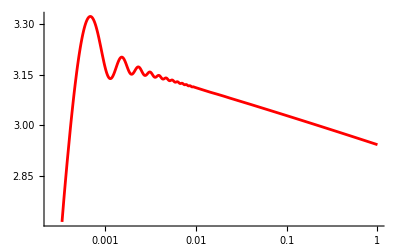

```mathematica
LogLinearPlot[{Log[(10^10)Psqz[k]]},{k,2.5*10^-4,1},PlotStyle->{Red}]
```